### Lotka-Volterra model for competing species.

```mathematica
(*manipulate with stab analysis*)
```

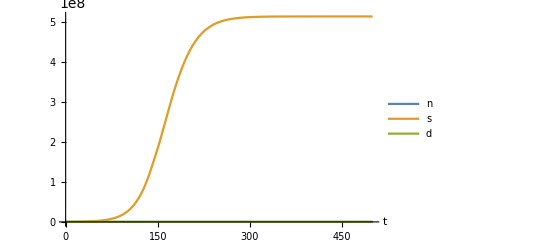

```mathematica
(*maybe restart Mathematica before*)
(*right hand sides of differential equations*)
Clear[pars, vars]
rhs[{n_,s_,d_}][{ϕ_, Ys_, Us_, hs_, ms_, δ_, xreq_, Kd_, r_}]:=
{
d*ϕ - (1/Ys)*((Us*n*s)/(1+Us*hs*n)),
(((Us*n*s)/(1+Us*hs*n)) - ms*s),
(r  (((s δ )/xreq)/(1+(s δ )/xreq)))*d*(1-d/Kd)
};
(*state variables*)
vars={n,s,d};
(*parameters*)
(*define standard set of parameters*)
pars={ϕ =85.714, Ys = 300, Us = 1176000, hs =  0.000167, ms = 0.05, δ = 2, xreq = 100000, Kd = 1000, r = 0.05};
(*parameteres for simulation*)
n0=1;s0=1; d0=1;tmax=500;
(*simulation*)
(*differential equations*)
eqs={{n'[t],s'[t], d'[t]}==rhs[{n[t],s[t], d[t]}][pars]};
(*initial conditions*)
inis=
{
n[0]==n0,
s[0]==s0,
d[0] == d0
};
(*state variables*)
vars={n,s,d};
(*solve the system of differential equations numerically*)
sol=NDSolve[
(*differential equations and initial conditions*)
Join[eqs,inis],
(*state variables*)
vars,
(*time span*)
{t,0,tmax},
Method -> "StiffnessSwitching"
];
(*plot simulation*)
Plot[
(*population densities*)
{
n[t]/.sol,
s[t]/.sol,
d[t]/.sol
},
(*time span*)
{t,0,tmax},
(*style*)
PlotLegends->{"n","s","d"},
AxesLabel->{"t"}

]
```

```mathematica
(*solve the equilibrium for a given set of parameters*)
solveeq[pars_,conditions_]:=NSolve[Join[{rhs[vars][pars]=={0,0,0}},conditions],{n,s,d}];
(*test it, there are multiple equilibria: both species present, only one species present, both species absent*)
solveeq[pars,{}]
```

{{n→4.25174×10^-8,d→1000.,s→5.14284×10^8},{n→4.25174×10^-8,d→-1.00389×10^-8+2.1549×10^-8 ⅈ,s→-0.00516283+0.0110823 ⅈ},{n→4.25174×10^-8,d→8.62728×10^-9-1.63112×10^-8 ⅈ,s→0.00443687-0.00838858 ⅈ}}

```mathematica
(*get only the positive equilibrium*)
solveeq[pars,{n>0,s>0, d >0}]
```

{{n→4.25174×10^-8,d→1000.,s→5.14284×10^8}}

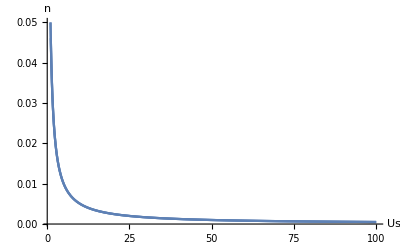

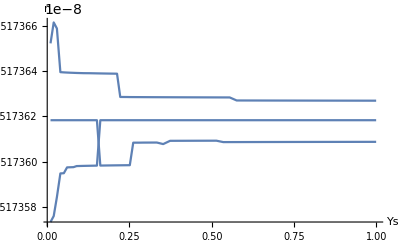

-Graphics-

```mathematica
(*now do the bifurcation, with say the parameter k1.*)
Plot[n/.solveeq[{ϕ, Ys, Usx, hs, ms, δ, xreq, Kd, r},{}],{Usx,1,100},PlotRange->Full,AxesLabel->{"Us","n"}]
Plot[n/.solveeq[{ϕ, Ysx, Us, hs, ms, δ, xreq, Kd, r},{}],{Ysx,0.01,1},PlotRange->Full,AxesLabel->{"Ys","n"}]
```

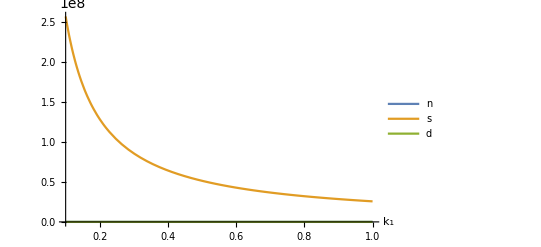

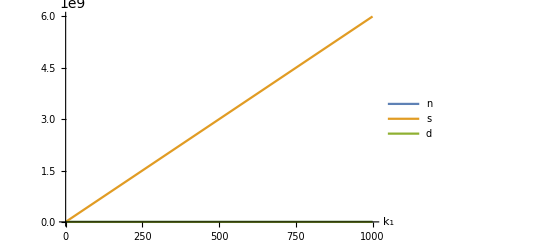

```mathematica
(*show both species. Only the equilibrium with both species present. When  k1 is big, the second species is getting outcompeted. I'm still trying to figure out how to call solveeq only once while still getting the colors right.*)
Plot[{
n/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}],
s/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}],
d/.solveeq[{ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r},{n>0,s>0, d >0}]
},
{msx,0.1,1},PlotRange->Full,AxesLabel->{"k_1"},PlotLegends->{"n","s", "d"}]

Plot[{
n/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}],
s/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}],
d/.solveeq[{ϕx, Ys, Us, hs, ms, δ, xreq, Kd, r},{n>0,s>0, d >0}]
},
{ϕx,0, 1000},PlotRange->Full,AxesLabel->{"k_1"},PlotLegends->{"n","s", "d"}]
```

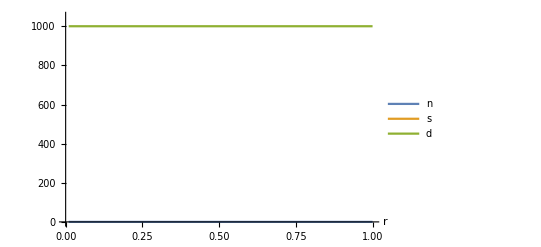

```mathematica
Plot[{
n/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}],
s/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}],
d/.solveeq[{ϕ, Ys, Us, hs, ms, δ, xreq, Kd, rx},{n>0,s>0, d >0}]
},
{rx,0.01, 1},PlotRange->{0,1050},AxesLabel->{"r"},PlotLegends->{"n","s", "d"}]
```

```mathematica
(*stability? Eigenvalues of Jacobian Matrix*)
```

```mathematica
(*the jacobi matrix*)
jacobi[vars_,pars_]:=Table[D[rhs[vars][pars],var],{var,vars}];
(*example with example pars*)
(*from left to right:
equilibrium,
jacobi matrix,
eigenvalues,
max real part (all eigenvector in this example are real),
stability of equilibrium (unstable <-> Max@Re@Eigenvalue > 0)*)
Grid[
Table[
With[{j=jacobi[vars,pars]/.eq},
{
eq,
j//MatrixForm,
Eigenvalues@j,
Max@Re[Eigenvalues@j],
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,Evaluate@solveeq[pars,{}]}],
Frame->All]
```

{n→4.25174×10^-8,d→1000.,s→5.14284×10^8} | (-2.01596×10^12 | 6.04788×10^14 | 0
-0.000166667 | 0. | 2.09841×10^-27
85.714 | 0 | -0.0499951) | {-2.01596×10^12,-0.05,-0.0499951} | -0.0499951 | Stable
{n→4.25174×10^-8,d→-1.00389×10^-8+2.1549×10^-8 ⅈ,s→-0.00516283+0.0110823 ⅈ} | (20.2379-43.4419 ⅈ | -6071.38+13032.6 ⅈ | 0
-0.000166667 | -1.39516×10^-10 | -1.00389×10^-14+2.1549×10^-14 ⅈ
85.714 | 0 | -5.16283×10^-9+1.10823×10^-8 ⅈ) | {20.2879-43.4419 ⅈ,-0.0499779+0.0000471913 ⅈ,-1.03256×10^-8+2.21646×10^-8 ⅈ} | 20.2879 | Unstable
{n→4.25174×10^-8,d→8.62728×10^-9-1.63112×10^-8 ⅈ,s→0.00443687-0.00838858 ⅈ} | (-17.3922+32.8827 ⅈ | 5217.67-9864.81 ⅈ | 0
-0.000166667 | 1.11408×10^-10 | 8.62728×10^-15-1.63112×10^-14 ⅈ
85.714 | 0 | 4.43687×10^-9-8.38858×10^-9 ⅈ) | {-17.3422+32.8828 ⅈ,-0.0500313-0.000059549 ⅈ,8.87375×10^-9-1.67772×10^-8 ⅈ} | 8.87375×10^-9 | Unstable

```mathematica
(*Make bifurcation of parameter k1 with stability analysis.*)
list=
Table[{msx,
With[{p={ϕ, Ys, Us, hs, msx, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{msx,0,0.99,0.01}];
```

```mathematica
(*now we have a list of this structure*)
list[[1;;3]]
```

{{0.,{{{n→0,d→0,s→-13086.4-11330.5 ⅈ},Unstable}}},{0.01,{{{n→8.50342×10^-9,d→1000.,s→2.57142×10^9},Stable},{{n→8.50342×10^-9,d→-1.90919×10^-9+4.38719×10^-9 ⅈ,s→-0.00490934+0.0112813 ⅈ},Unstable},{{n→8.50342×10^-9,d→1.76642×10^-9-3.15444×10^-9 ⅈ,s→0.0045422-0.00811139 ⅈ},Unstable}}},{0.02,{{{n→1.70069×10^-8,d→1000.,s→1.28571×10^9},Stable},{{n→1.70069×10^-8,d→-5.81613×10^-9+1.29062×10^-8 ⅈ,s→-0.00747786+0.0165936 ⅈ},Unstable},{{n→1.70069×10^-8,d→5.17294×10^-9-9.51536×10^-9 ⅈ,s→0.0066509-0.012234 ⅈ},Unstable}}}}

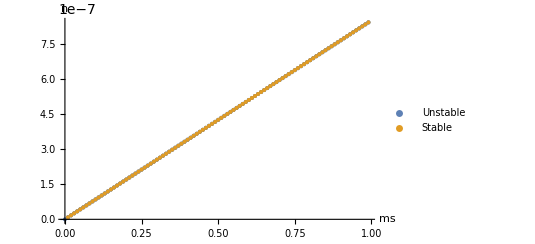
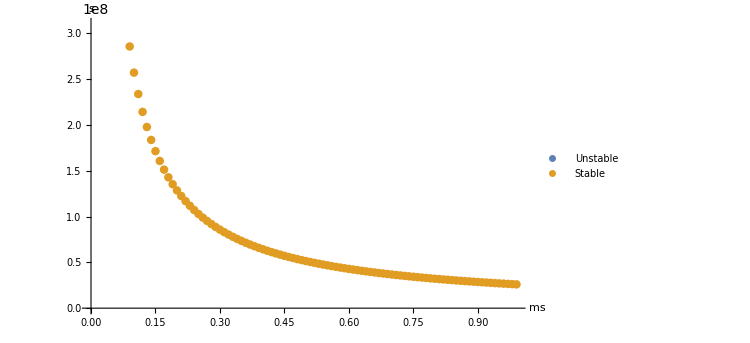
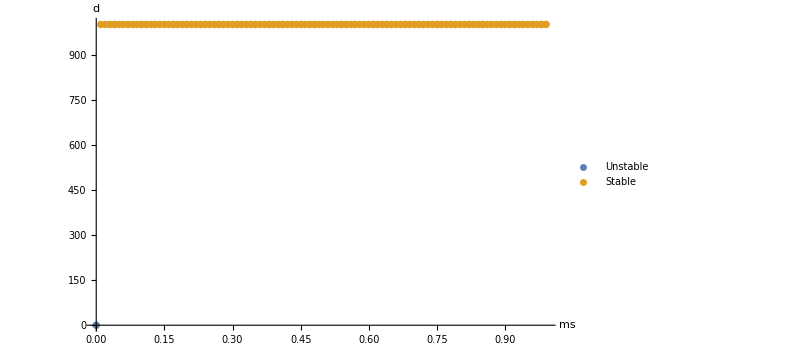

```mathematica
(*Plot: extract the Stable and Unstable equilibria of the different species from list*)
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"ms",var}],{
var,vars}]
```

```mathematica
(*The results are rather intuitive, as we increase the mortality of the Bee we increase the stable equilibrium of the pollen, decrease the stable equilibrium of the bees, and the stability of the plants stays the same *recall the analytical solution of our equations suggest that the plants will have a stable equilibrium at Kd*  *)
```

{{64448,{{{n→7.75826×10^-7,d→1000.,s→5.14284×10^8},Stable},{{n→7.75826×10^-7,d→1.38235×10^-9+2.10525×10^-8 ⅈ,s→0.000710923+0.010827 ⅈ},Unstable},{{n→7.75826×10^-7,d→-2.29412×10^-10-1.80625×10^-8 ⅈ,s→-0.000117983-0.00928924 ⅈ},Unstable}}},{74448,{{{n→6.71615×10^-7,d→1000.,s→5.14284×10^8},Stable},{{n→6.71615×10^-7,d→1.38235×10^-9+2.10525×10^-8 ⅈ,s→0.000710923+0.010827 ⅈ},Unstable},{{n→6.71615×10^-7,d→-2.29412×10^-10-1.80625×10^-8 ⅈ,s→-0.000117983-0.00928924 ⅈ},Unstable}}},{84448,{{{n→5.92085×10^-7,d→1000.,s→5.14284×10^8},Stable},{{n→5.92085×10^-7,d→1.38235×10^-9+2.10525×10^-8 ⅈ,s→0.000710923+0.010827 ⅈ},Unstable},{{n→5.92085×10^-7,d→-2.29412×10^-10-1.80625×10^-8 ⅈ,s→-0.000117983-0.00928924 ⅈ},Unstable}}}}

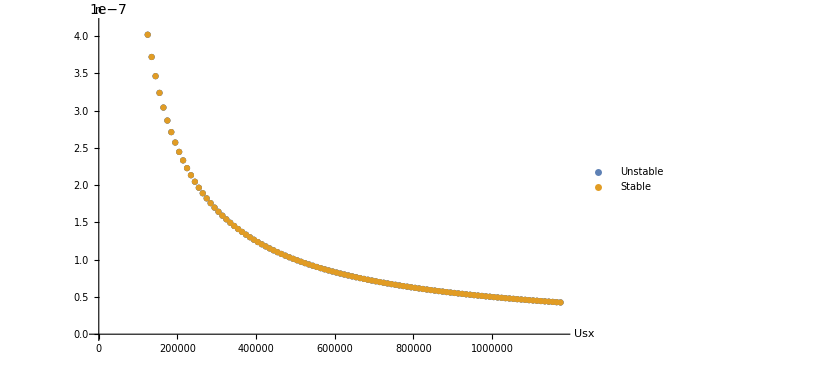
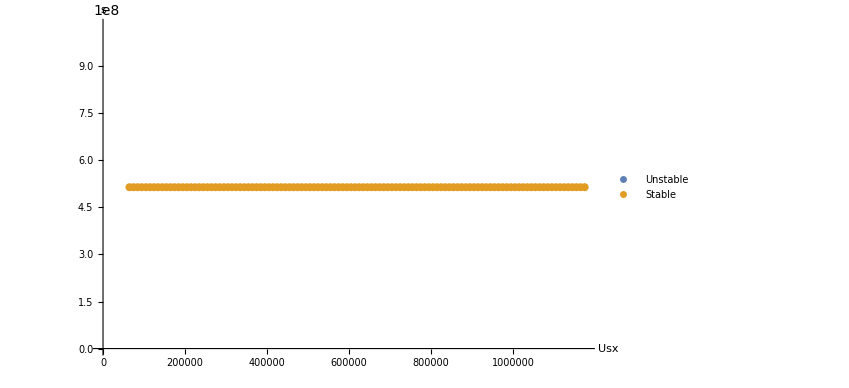
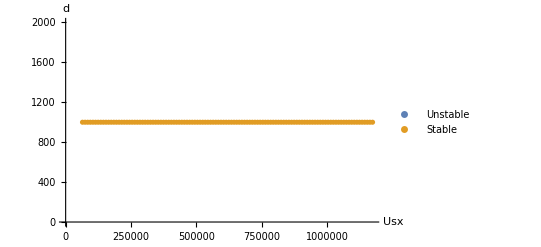

```mathematica
(*Make bifurcation of parameter k1 with stability analysis.*)
list=
Table[{Usx,
With[{p={ϕ, Ys, Usx, hs, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{Usx,64448,1176000,10000}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"Usx",var}],{
var,vars}]
```

```mathematica
(*Its a bit interesting that Uptake only affects the equilibrium of Pollen and nothing else. As expected, if we increase the uptake rate of the pollen by bees we decrease the stable equilibrium of the pollen.*)
```

{{0.000167,{{{n→4.25174×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→4.25174×10^-8,d→-1.00389×10^-8+2.1549×10^-8 ⅈ,s→-0.00516283+0.0110823 ⅈ},Unstable},{{n→4.25174×10^-8,d→8.62728×10^-9-1.63112×10^-8 ⅈ,s→0.00443687-0.00838858 ⅈ},Unstable}}},{0.010167,{{{n→4.25386×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→4.25386×10^-8,d→-9.79491×10^-9+2.02694×10^-8 ⅈ,s→-0.00503737+0.0104242 ⅈ},Unstable},{{n→4.25386×10^-8,d→1.29862×10^-8-2.48923×10^-8 ⅈ,s→0.00667862-0.0128017 ⅈ},Unstable}}},{0.020167,{{{n→4.25599×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→4.25599×10^-8,d→-9.15188×10^-9+1.88964×10^-8 ⅈ,s→-0.00470666+0.0097181 ⅈ},Unstable},{{n→4.25599×10^-8,d→1.20965×10^-8-2.32541×10^-8 ⅈ,s→0.00622102-0.0119592 ⅈ},Unstable}}}}

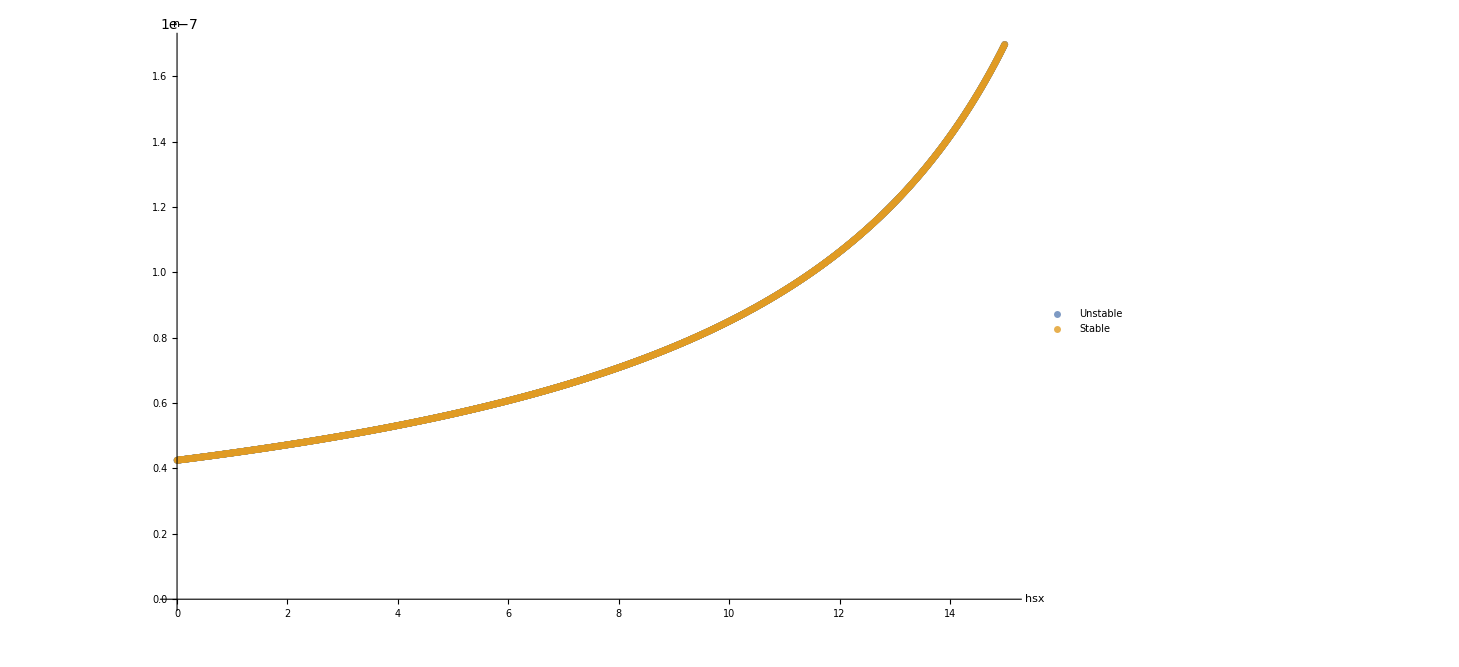
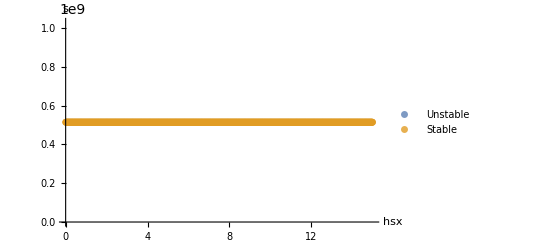
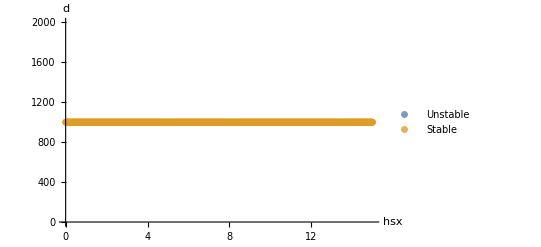

```mathematica
list=
Table[{hsx,
With[{p={ϕ, Ys, Us, hsx, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{hsx,0.000167,15,0.01}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"hsx",var},PlotMarkers->({Graphics`PlotMarkers[][[1,1]],7}),PlotStyle->{{Automatic,Opacity[.8]}}],{
var,vars}]
```

Power::infy: Infinite expression 1/0. encountered.

{{0.,{}},{0.01,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-1.88031×10^-10 ⅈ,d→-4.14925×10^-7+8.36045×10^-7 ⅈ,s→-4.14925×10^-6+8.36045×10^-6 ⅈ},Unstable},{{n→0.0111111+2.01413×10^-10 ⅈ,d→4.48469×10^-7-8.90871×10^-7 ⅈ,s→4.48469×10^-6-8.90871×10^-6 ⅈ},Unstable}}},{0.02,{{{n→0.0111111,d→1000.,s→20000.},Stable},{{n→0.0111111-1.85553×10^-10 ⅈ,d→-2.59262×10^-7+5.23283×10^-7 ⅈ,s→-5.18525×10^-6+0.0000104657 ⅈ},Unstable},{{n→0.0111111+1.51712×10^-10 ⅈ,d→2.14197×10^-7-4.25643×10^-7 ⅈ,s→4.28394×10^-6-8.51287×10^-6 ⅈ},Unstable}}}}

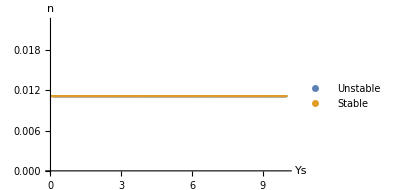
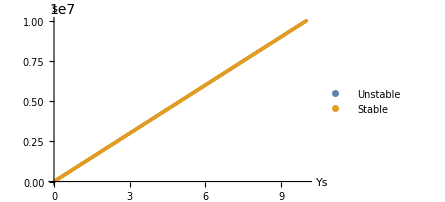
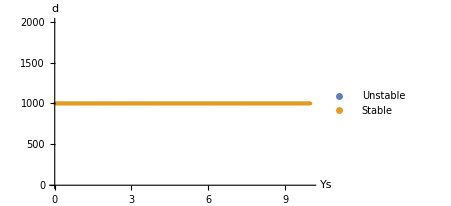

```mathematica
list=
Table[{Ysx,
With[{p={ϕ, Ysx, Us, hs, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{Ysx,0,10,0.01}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"ms",var}],{
var,vars}]
```

```mathematica
(*Yield doesnt affect stable equilibria of the plants nor pollen, but linearly increases the stable equilibria of our bees*)
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(69046 d)/57903+(40299 n)/38602-(142003 s)/115806 == 1.

{{0.,{{{n→0.95789,s→0.,d→0.},Unstable},{{n→0.0111111,s→-0.73462,d→-0.073462},Unstable}}},{0.2,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-4.02397×10^-10 ⅈ,d→-4.04403×10^-6+8.12137×10^-6 ⅈ,s→-0.0000404403+0.0000812137 ⅈ},Unstable},{{n→0.0111111+7.73321×10^-10 ⅈ,d→7.79877×10^-6-0.0000155537 ⅈ,s→0.0000779877-0.000155537 ⅈ},Unstable}}},{0.4,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111-4.12286×10^-10 ⅈ,d→-2.62545×10^-6+5.27752×10^-6 ⅈ,s→-0.0000262545+0.0000527752 ⅈ},Unstable},{{n→0.0111111+3.89853×10^-10 ⅈ,d→2.49435×10^-6-4.97049×10^-6 ⅈ,s→0.0000249435-0.0000497049 ⅈ},Unstable}}}}

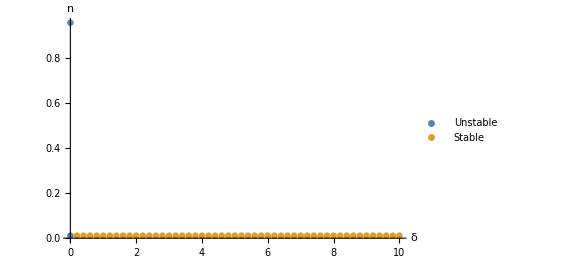
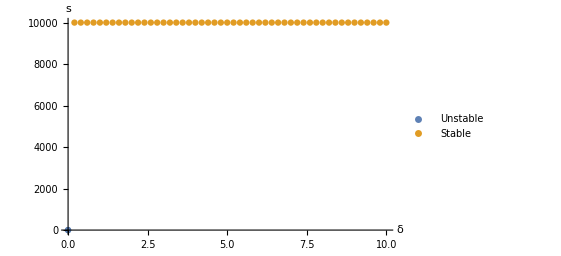
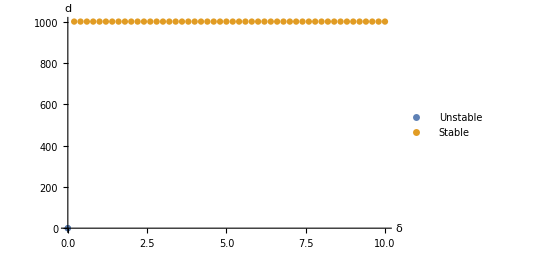

```mathematica
list=
Table[{δx,
With[{p={ϕ, Ys, Us, hs, ms, δx, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{δx,0,10,0.2}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"δ",var}],{
var,vars}]
```

```mathematica
(*Delta has no effect on the stable equilibria of our three state variables*)
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(69046 d)/57903+(40299 n)/38602-(142003 s)/115806 == 1.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

{{0.,{{{n→0.95789,s→0.,d→0.},Unstable},{{n→0.0111111,s→-0.73462,d→-0.073462},Unstable}}},{0.01,{{{s→0.,d→0.},If[Max[0,90. Re[((-0.0111111+1. n) (0.1+1. n))/(1.+10. n)^2]]>0,Unstable,Stable]},{{n→0.0111111,s→0.,d→0.},Stable},{{n→0.0111111,s→10000.,d→1000.},If[Max[-1. Re[δx/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx-√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx+√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)]]>0,Unstable,Stable]}}},{0.02,{{{s→0.,d→0.},If[Max[0,90. Re[((-0.0111111+1. n) (0.1+1. n))/(1.+10. n)^2]]>0,Unstable,Stable]},{{n→0.0111111,s→0.,d→0.},Stable},{{n→0.0111111,s→10000.,d→1000.},If[Max[-2. Re[δx/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx-√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)],1/2 Re[(-8.1×10^6-8.1×10^8 δx+√(6.561×10^13+1.3122×10^16 δx+6.561×10^17 δx^2))/(1.+100. δx)]]>0,Unstable,Stable]}}}}

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

Part::partd: Part specification m⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {m⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification l⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

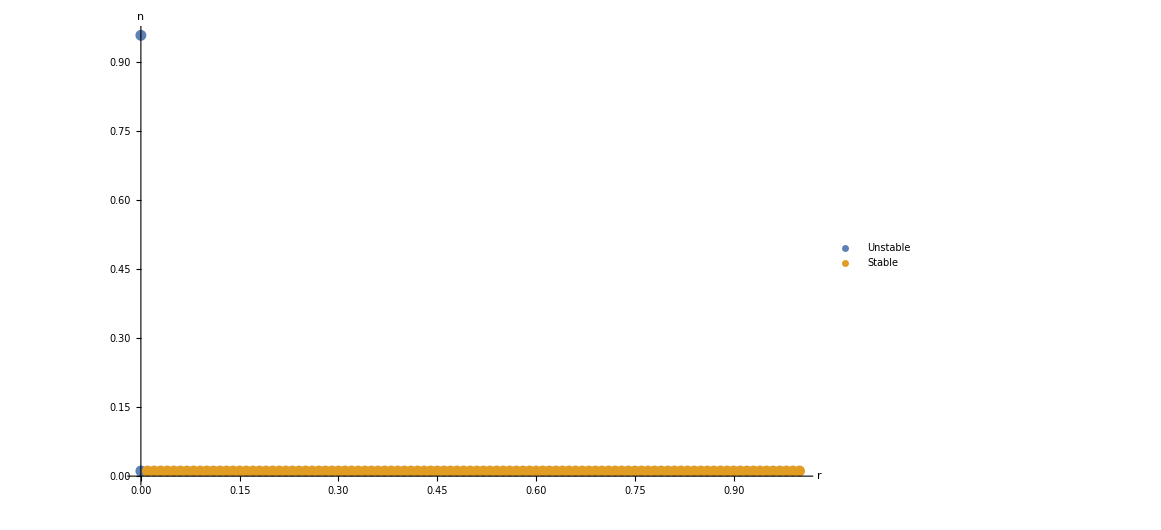
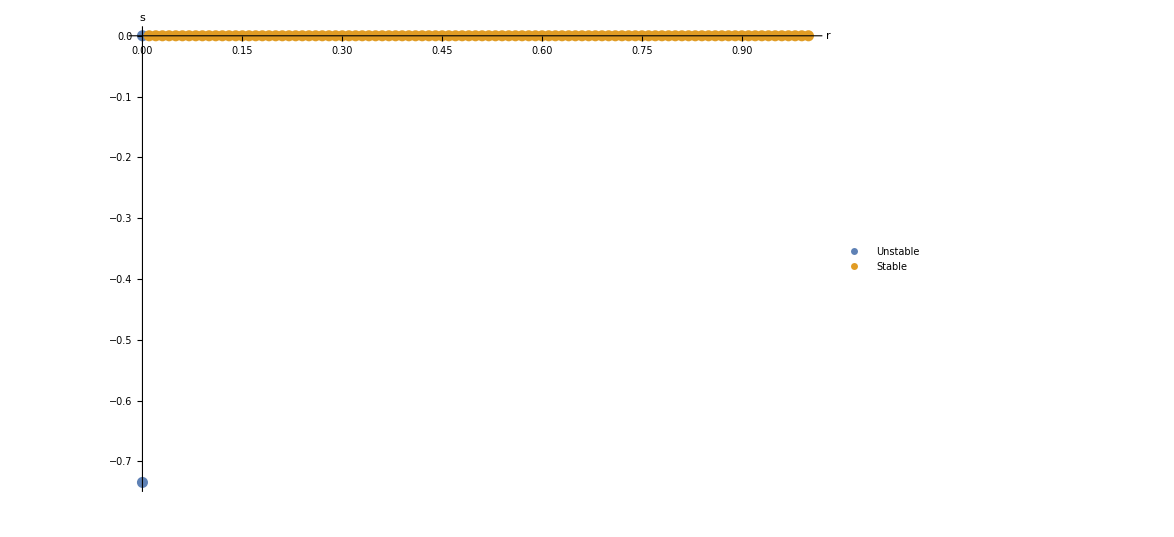
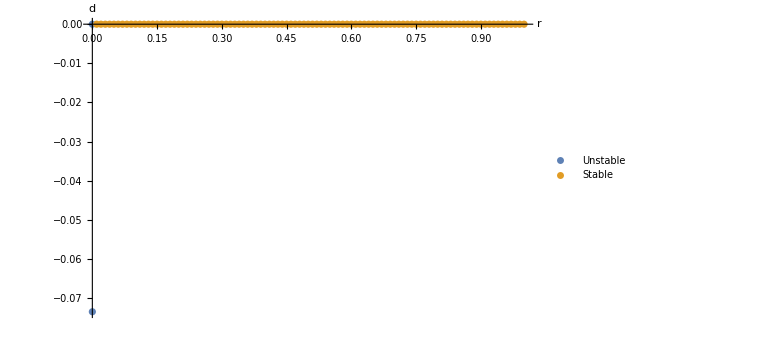

```mathematica
list=
Table[{rx,
With[{p={ϕ, Ys, Us, hs, ms, δx, xreq, Kd, rx}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{rx,0,1,0.01}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"r",var}],{
var,vars}]
```

```mathematica
(*Basically doesn't affect the system unless reproduction is waaaay to small. *)
```

{{1,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-4.24064×10^-9+8.72825×10^-9 ⅈ,s→-4.24064×10^-8+8.72825×10^-8 ⅈ},Unstable},{{n→0.0111111,d→7.74172×10^-9-1.51077×10^-8 ⅈ,s→7.74172×10^-8-1.51077×10^-7 ⅈ},Unstable}}},{2,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-1.36054×10^-8+2.78465×10^-8 ⅈ,s→-1.36054×10^-7+2.78465×10^-7 ⅈ},Unstable},{{n→0.0111111,d→1.23397×10^-8-2.42028×10^-8 ⅈ,s→1.23397×10^-7-2.42028×10^-7 ⅈ},Unstable}}},{3,{{{n→0.0111111,d→1000.,s→10000.},Stable},{{n→0.0111111,d→-1.79324×10^-8+3.66018×10^-8 ⅈ,s→-1.79324×10^-7+3.66018×10^-7 ⅈ},Unstable},{{n→0.0111111,d→1.62132×10^-8-3.18789×10^-8 ⅈ,s→1.62132×10^-7-3.18789×10^-7 ⅈ},Unstable}}}}

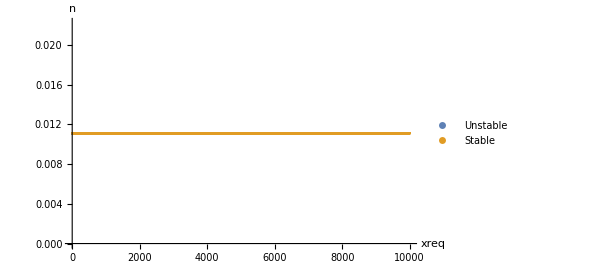
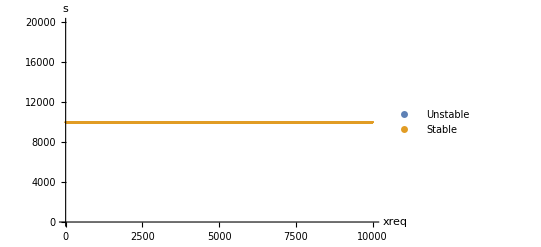
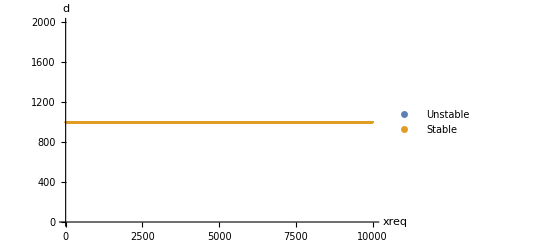

```mathematica
list=
Table[{xreqx,
With[{p={ϕ, Ys, Us, hs, ms, δ, xreqx, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{xreqx,1,10000,1}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"xreq",var}],{
var,vars}]
```

```mathematica
(*Does not affect the stable equilibria of the system*)
```

{{1,{{{n→4.47547×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→4.47547×10^-8,d→-1.43018×10^-8+2.93258×10^-8 ⅈ,s→-0.00735517+0.0150818 ⅈ},Unstable},{{n→4.47547×10^-8,d→1.29986×10^-8-2.54528×10^-8 ⅈ,s→0.00668497-0.01309 ⅈ},Unstable}}},{2,{{{n→4.72411×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→4.72411×10^-8,d→-1.33468×10^-8+2.73228×10^-8 ⅈ,s→-0.00686406+0.0140517 ⅈ},Unstable},{{n→4.72411×10^-8,d→1.2108×10^-8-2.37439×10^-8 ⅈ,s→0.00622693-0.0122111 ⅈ},Unstable}}},{3,{{{n→5.002×10^-8,d→1000.,s→5.14284×10^8},Stable},{{n→5.002×10^-8,d→-1.28177×10^-8+2.62157×10^-8 ⅈ,s→-0.00659192+0.0134823 ⅈ},Unstable},{{n→5.002×10^-8,d→1.16159×10^-8-2.27975×10^-8 ⅈ,s→0.00597386-0.0117244 ⅈ},Unstable}}}}

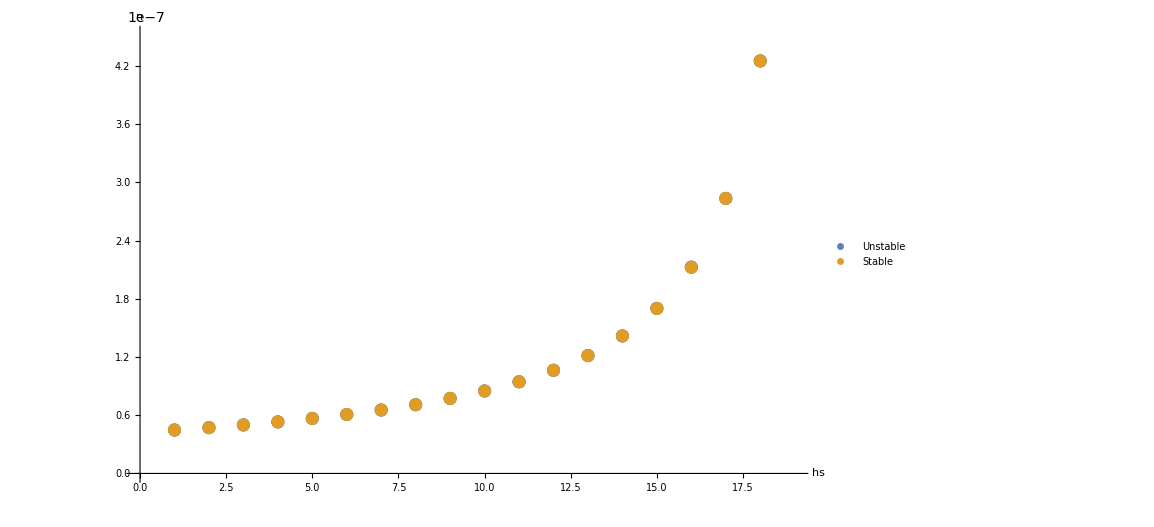
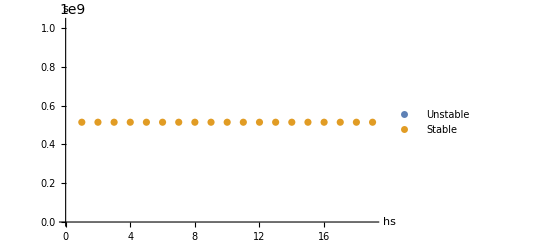
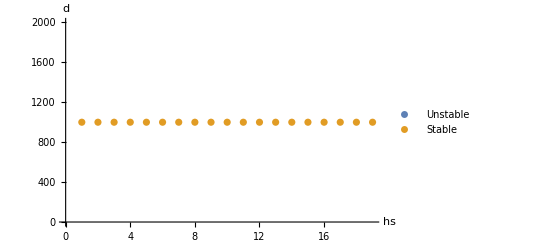

```mathematica
list=
Table[{hsx,
With[{p={ϕ, Ys, Us, hsx, ms, δ, xreq, Kd, r}},
Table[
With[{j=jacobi[vars,p]/.eq},
{
eq,
If[Max@Re[Eigenvalues@j]>0,"Unstable","Stable"]
}
],
{eq,solveeq[p,{}]}]]},{hsx,1,20,1}];
list[[1;;3]]
stability={"Unstable","Stable"};
Column@Table[ListPlot[Table[Flatten[Table[Table[If[m[[2]]==stab,{l[[1]],var/.m[[1]]},Nothing],{m,l[[2]]}],{l,list}],1],{stab,stability}],PlotLegends->stability,AxesLabel->{"hs",var}],{
var,vars}]
```

```mathematica
(*THere is a vertical asymptote at hs=10, once we surpass this we enter negative pollen land*)
```